```mathematica
p[r_]:=a (r+c)^b
```

```mathematica
Clear[p,a,b]
```

```mathematica
b=-2;
```

```mathematica
a=1/(56 π G);
```

```mathematica
c=0;
```

```mathematica
Assuming[a>0&&b>-3,FullSimplify[r^2 D[p[r],r]==-16 π G p[r] (p[r] r^3+3 ∫_0^r (p[q] q^2)ⅆq)/(1-(24 π G)/r∫_0^r (p[q] q^2)ⅆq)]]
```

a b r^(1+b)==-(16 a^2 (6+b) G π r^(3+2 b))/(3+b-24 a G π r^(2+b))

```mathematica
1/(1-(24 π G)/r∫_0^r (p[q] q^2)ⅆq)//FullSimplify
```

7/4

```mathematica
B=7/4;
```

```mathematica
DSolve[1/B-1+r/(2 B)D[A[r],r]/A[r]==-8 π G a,A[r],r]
```

{{A[r]→r C[1]}}

```mathematica
Clear[A]
```

```mathematica
A[r_]:=k r
```

```mathematica
(* Check for R11 *)
```

```mathematica
D[A[r],{r,2}]/(2 A[r])-D[A[r],r]/(4 A[r])(D[A[r],r]/A[r])==-8 π G p[r] B
```

True

```mathematica
-D[A[r],{r,2}]/(2 B)+D[A[r],r]/(4 B)D[A[r],r]/A[r]-D[A[r],r]/(r B)==-3*8 π G p[r] A[r]
```

True

```mathematica
-A2/(2 B)+A1/(4 B)(A1/A+B1/B)-A1/(r B)==-3*8 π p[r] A+Λ A
```

```mathematica
A2/(2 A)-A1/(4 A)(A1/A+B1/B)-B1/(r B)==-8 π p[r] B+Λ B
```

```mathematica
1/B-1+r/(2 B)(A1/A-B1/B)==-8 π p[r] r^2+Λ r^2
```

```mathematica
Eliminate[{-A2/(2 B)+A1/(4 B)(A1/A+B1/B)-A1/(r B)==-3*8 π p[r] A+Λ A,1/B-1+r/(2 B)(A1/A-B1/B)==-8 π p[r] r^2+Λ r^2},{A2}]
```

B1==B (A1/A+2/r-(2 B)/r-2 B r Λ+16 B π r p[r])&&A≠0&&B≠0&&r≠0

```mathematica
Eliminate[{-A2/(2 B)+A1/(4 B)(A1/A+B1/B)-A1/(r B)==-3*8 π p[r] A+Λ A,A2/(2 A)-A1/(4 A)(A1/A+B1/B)-B1/(r B)==-8 π p[r] B+Λ B},{A2}]
```

B1==B (-A1/A-2 B r Λ+32 B π r p[r])&&A≠0&&B≠0&&r≠0

```mathematica
Assuming[B>0,FullSimplify[B (A1/A+2/r-(2 B)/r-2 B r Λ+16 B π r p[r])==B (-A1/A-2 B r Λ+32 B π r p[r])]]
```

(-1+B)/r+8 B π r p[r]==A1/A

```mathematica
-A''[r]/(2 B[r])+A'[r]/(4 B[r])(A'[r]/A[r]+B'[r]/B[r])-A'[r]/(r B[r])==-3*8 π p[r] A[r]+Λ A[r]
```

```mathematica
A''[r]/(2 A[r])-A'[r]/(4 A[r])(A'[r]/A[r]+B'[r]/B[r])-B'[r]/(r B[r])==-8 π p[r] B[r]+Λ B[r]
```

```mathematica
1/B[r]-1+r/(2 B[r])(A'[r]/A[r]-B'[r]/B[r])==-8 π p[r] r^2+Λ r^2
```

```mathematica
Eliminate[{-A''[r]/(2 B[r])+A'[r]/(4 B[r])(A'[r]/A[r]+B'[r]/B[r])-A'[r]/(r B[r])==-3*8 π p[r] A[r]+Λ A[r],A''[r]/(2 A[r])-A'[r]/(4 A[r])(A'[r]/A[r]+B'[r]/B[r])-B'[r]/(r B[r])==-8 π p[r] B[r]+Λ B[r]},{A''[r]}]
```

B'[r]==B[r] (-2 r Λ B[r]+32 π r B[r] p[r]-A'[r]/A[r])&&r≠0&&A[r]≠0&&B[r]≠0

```mathematica
Eliminate[{-A''[r]/(2 B[r])+A'[r]/(4 B[r])(A'[r]/A[r]+B'[r]/B[r])-A'[r]/(r B[r])==-3*8 π p[r] A[r]+Λ A[r],1/B[r]-1+r/(2 B[r])(A'[r]/A[r]-B'[r]/B[r])==-8 π p[r] r^2+Λ r^2},{A''[r]}]
```

B'[r]==B[r] (2/r-(2 B[r])/r-2 r Λ B[r]+16 π r B[r] p[r]+A'[r]/A[r])&&r≠0&&A[r]≠0&&B[r]≠0

```mathematica
Assuming[B[r]>0,FullSimplify[B[r] (2/r-(2 B[r])/r-2 r Λ B[r]+16 π r B[r] p[r]+A'[r]/A[r])==B[r] (-2 r Λ B[r]+32 π r B[r] p[r]-A'[r]/A[r])]]
```

(-1+B[r])/r+8 π r B[r] p[r]==A'[r]/A[r]

```mathematica
D[(-1+B[r])/r+8 π r B[r] p[r]==A'[r]/A[r],r]//FullSimplify
```

(1+(r+8 π r^3 p[r]) B'[r]+B[r] (-1+8 π r^2 (p[r]+r p'[r])))/r^2==(-A'[r]^2+A[r] A''[r])/A[r]^2

```mathematica
Eliminate[{(1+(r+8 π r^3 p[r]) B'[r]+B[r] (-1+8 π r^2 (p[r]+r p'[r])))/r^2==(-A'[r]^2+A[r] A''[r])/A[r]^2,-A''[r]/(2 B[r])+A'[r]/(4 B[r])(A'[r]/A[r]+B'[r]/B[r])-A'[r]/(r B[r])==-3*8 π p[r] A[r]+Λ A[r],A''[r]/(2 A[r])-A'[r]/(4 A[r])(A'[r]/A[r]+B'[r]/B[r])-B'[r]/(r B[r])==-8 π p[r] B[r]+Λ B[r],1/B[r]-1+r/(2 B[r])(A'[r]/A[r]-B'[r]/B[r])==-8 π p[r] r^2+Λ r^2},{A''[r],A'[r],B'[r]}]
```

8 π p'[r]==-Λ/r+(Λ B[r])/r+(16 π p[r])/r-(16 π B[r] p[r])/r+8 π r Λ B[r] p[r]-128 π^2 r B[r] p[r]^2&&r≠0&&A[r]≠0&&B[r]≠0

```mathematica
(* TOV WITHOUT LAMBDA *)
```

```mathematica
B[r_,Λ_]=(1-(2 m[r])/r+(2 Λ r^2)/3)^-1;
```

```mathematica
8 π p'[r]==-Λ/r+(Λ B[r,0])/r+(16 π p[r])/r-(16 π B[r,0] p[r])/r+8 π r Λ B[r,0] p[r]-128 π^2 r B[r,0] p[r]^2/.Λ->0//FullSimplify
```

(4 p[r] (m[r]+4 π r^3 p[r]))/(r (r-2 m[r]))+p'[r]==0

```mathematica
(* TOV WITH LAMBDA *)
```

```mathematica
8 π p'[r]==-Λ/r+(Λ B[r,Λ])/r+(16 π p[r])/r-(16 π B[r,Λ] p[r])/r+8 π r Λ B[r,Λ] p[r]-128 π^2 r B[r,Λ] p[r]^2//FullSimplify
```

((Λ-16 π p[r]) (-3 m[r]+r^3 (Λ-12 π p[r])))/(r (3 r+2 r^3 Λ-6 m[r]))+4 π p'[r]==0

```mathematica
DSolve[a[r]+b[r] p[r]+c[r] p[r]^2+4 π p'[r]==0,p[r],r]
```

DSolve[a[r]+b[r] p[r]+c[r] p[r]^2+4 π p'[r]==0,p[r],r]

```mathematica
Solve[((Λ-16 π 0) (-3 M+r^3 (Λ-12 π 0)))/(r (3 r+2 r^3 Λ-6 M))+4 π p'==0,p']//FullSimplify
```

{{p'→-(Λ (-3 M+r^3 Λ))/(4 π r (-6 M+3 r+2 r^3 Λ))}}

```mathematica
(* NUMERICAL SOLUTION *)
```

```mathematica
p[r_]:=1/(12 π r^2)D[m[r],r]
```

```mathematica
mppbc[r_]:=-1/(12 π r^2) (Λ (-3 M+r^3 Λ))/(4 π r (-6 M+3 r+2 r^3 Λ))
```

```mathematica
Assuming[r>0,FullSimplify[((Λ-16 π p[r]) (-3 m[r]+r^3 (Λ-12 π p[r])))/(r (3 r+2 r^3 Λ-6 m[r]))+4 π p'[r]==0]]
```

(-2 m'[r]+((3 r^2 Λ-4 m'[r]) (r^3 Λ-3 m[r]-r m'[r]))/(3 r+2 r^3 Λ-6 m[r])+r m''[r])/(3 r^3)==0

```mathematica
-2 m'[r]+((3 r^2 Λ-4 m'[r]) (r^3 Λ-3 m[r]-r m'[r]))/(3 r+2 r^3 Λ-6 m[r])+r m''[r]==0
```

((3 r^2 Λ-4 m'[r]) (r^3 Λ-3 m[r]-r m'[r]))/(3 r+2 r^3 Λ-6 m[r])+r m''[r]==2 m'[r]

{{m→InterpolatingFunction[{{0.001,2.}},<>]}}

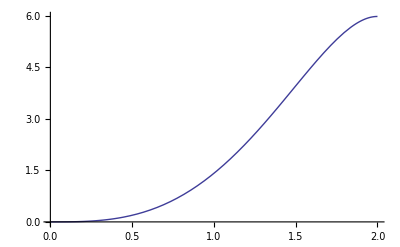

```mathematica
Clear[Λ,ϵ,R]
Λ=10;ϵ=0.001;R=2;
s=NDSolve[{((3 r^2 Λ-4 m'[r]) (r^3 Λ-3 m[r]-r m'[r]))/(3 r+2 r^3 Λ-6 m[r])+r m''[r]==2 m'[r],m[ϵ]==ϵ^2,m'[R]==0},m,{r,ϵ,R}]
Plot[Evaluate[m[r]/.s],{r,ϵ,R},PlotRange->All]
```

```mathematica
pr=Table[Flatten[{r,1/(12 π r^2)Evaluate[m'[r]/.s]}],{r,ϵ,R,R/1000}];
```

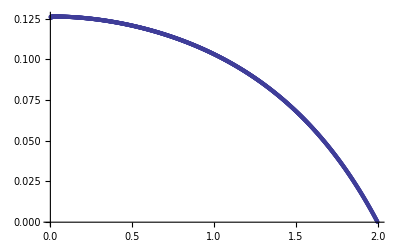

```mathematica
ListPlot[pr,AxesOrigin->{0,0}]
```

```mathematica
Fit[pr,{1,r,r^2,r^3,r^4,r^5,r^6},r]
```

0.126207+0.00156926 r-0.030149 r^2+0.0153509 r^3-0.0136275 r^4+0.00489575 r^5-0.00109678 r^6

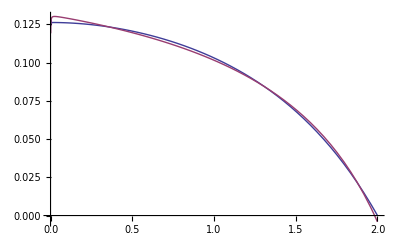

```mathematica
Plot[{1/(12 π r^2)Evaluate[m'[r]/.s]},{r,ϵ,R},AxesOrigin->{0,0}]
```

{{2.4612×10^-10,1},{1.3882×10^-8,2},{1.55963×10^-7,3},{8.7319×10^-7,4},{3.32603×10^-6,5},{9.92271×10^-6,6},{0.0000250041,7},{0.0000556782,8},{0.000112803,9},{0.000212115,10},{0.000375502,11},{0.000632419,12},{0.00102144,13},{0.00159196,14},{0.002406,15},{0.00354018,16},{0.00508777,17},{0.00716094,18},{0.00989303,19},{0.013441,20},{0.0179881,21},{0.0237461,22},{0.0309586,23},{0.0399036,24},{0.0508962,25},{0.0642921,26},{0.08049,27},{0.0999356,28},{0.123124,29},{0.150603,30},{0.182978,31},{0.220912,32},{0.265133,33},{0.316433,34},{0.375676,35},{0.443798,36},{0.52181,37},{0.610805,38},{0.711958,39},{0.826529,40},{0.955869,41},{1.10142,42},{1.26472,43},{1.4474,44},{1.65121,45},{1.87797,46},{2.12964,47},{2.40826,48},{2.71601,49},{3.05515,50},{3.42807,51},{3.83727,52},{4.28537,53},{4.77509,54},{5.30929,55},{5.89091,56},{6.52305,57},{7.20888,58},{7.9517,59},{8.75493,60},{9.62209,61},{10.5568,62},{11.5627,63},{12.6437,64},{13.8037,65},{15.0466,66},{16.3766,67},{17.7976,68},{19.314,69},{20.9299,70},{22.6496,71},{24.4774,72},{26.4176,73},{28.4745,74},{30.6523,75},{32.9553,76},{35.3877,77},{37.9534,78},{40.6566,79},{43.5011,80},{46.4906,81},{49.6285,82},{52.9182,83},{56.3628,84},{59.9649,85},{63.727,86},{67.6512,87},{71.7391,88},{75.992,89},{80.4103,90},{84.9944,91},{89.7436,92},{94.6567,93},{99.7317,94},{104.966,95},{110.355,96},{115.896,97},{121.581,98},{127.404,99},{133.357,100}}

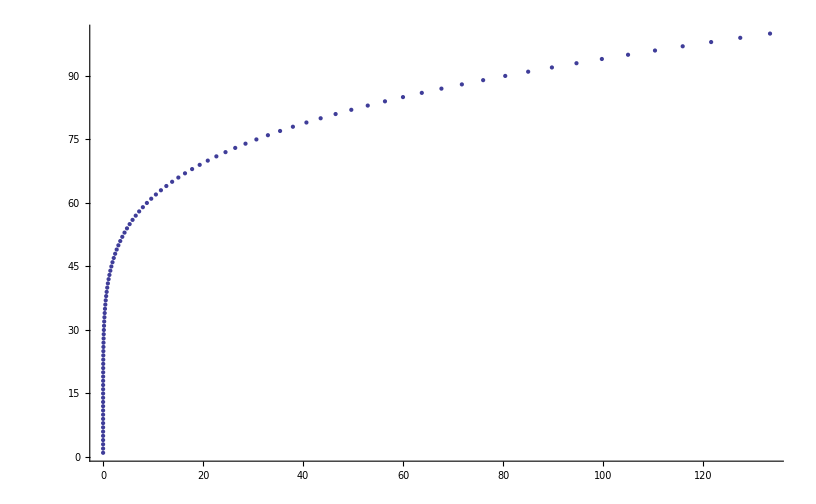

```mathematica
nmax=100;
pres=Table[Flatten[{NIntegrate[4 π r^2 Evaluate[m[r]/.s],{r,ϵ,n/nmax R}],n}],{n,1,nmax}]
ListPlot[pres,PlotRange->All]
Clear[nmax]
```

```mathematica
(* ANALYTIC SOLUTION *)
```

```mathematica
Clear[Λ,m]
```

```mathematica
m[r_]:=Subscript[a, i] r^i
```

```mathematica
m'[r]
```

i r^(-1+i) a_i

```mathematica
((3 r^2 Λ-4 m'[r]) (r^3 Λ-3 m[r]-r m'[r]))/(3 r+2 r^3 Λ-6 m[r])+r m''[r]==2 m'[r]//FullSimplify
```

(3 r^6 Λ^2+r^i a_i (3 (-3+i) i r+(-9+i (-13+2 i)) r^3 Λ-2 (-15+i) i r^i a_i))/(r (3 r+2 r^3 Λ-6 r^i a_i))==0

```mathematica
Series[3 r^6 Λ^2+r^i Subscript[a, i] (3 (-3+i) i r+(-9+i (-13+2 i)) r^3 Λ-2 (-15+i) i r^i Subscript[a, i])==0,{r,0,6}]
```

(3 Λ^2 r^6+O[r]^7)+r^i (3 (-3 i+i^2) a_i r+(-9 Λ-13 i Λ+2 i^2 Λ) a_i r^3+O[r]^7)+30 i r^(2 i) a_i^2-2 i^2 r^(2 i) a_i^2==0

```mathematica
3 r^6 Λ^2+r^i Subscript[a, i] (3 (-3+i) i r+(-9+i (-13+2 i)) r^3 Λ-2 (-15+i) i r^i Subscript[a, i])==0//Expand
```

3 r^6 Λ^2-9 i r^(1+i) a_i+3 i^2 r^(1+i) a_i-9 r^(3+i) Λ a_i-13 i r^(3+i) Λ a_i+2 i^2 r^(3+i) Λ a_i+30 i r^(2 i) a_i^2-2 i^2 r^(2 i) a_i^2==0